TRIKOTNIKI

V tej seminarski nalogi bom opisala značilnosti za vse spodaj naštete trikotnike. Zraven bom napisala tudi formule za izračun obsegov in ploščin. Kjer je možno, bom napisala tudi formule za izračun polmerov očrtane in včrtane krožnice v trikotniku.  Za lažjo predstavo bom trikotnike narisala. Povedala bom tudi kaj je težiščnica. Na koncu pa bom vse to ponazorila še s kakšno nalogo.

Trikotniki so eni najbolj osnovnih geometrijskih likov. Kot lahko razberemo že iz imena imajo tri kote, tri ogišča in seveda tudi tri stranice. Poznamo več vrst trikotnikov, razlikujemo pa jih glede na stranice. Delimo jih na pravokotne, enakostranične, enakokrake in poljubne. Vsota notranjih kotov v trikotniku je vedno enaka 180 °, vsota zunanjih kotov pa je enaka 360 °. Med ogliščema A in B je stranica c, med ogliščema B in C je stranica a, med ogliščema A in C pa je stranica b. Pri oglišču A se nahaja kot α (alfa), pri oglišču B se nahaja kot β (beta), pri oglišču C pa je kot γ (gama).
      
1. PRAVOKOTNI TRIKOTNIK

Trikotnik[{0,0},{4,1},{3,5}]

{Daljica[{0,0},{4,1}],Daljica[{4,1},{3,5}],Daljica[{3,5},{0,0}]}

{Kot[{3,5},{0,0},{4,1}],Kot[{0,0},{4,1},{3,5}],Kot[{4,1},{3,5},{0,0}]}

{Point[{0,0}],Point[{4,1}],Point[{3,5}]}

{Line[{{0,0},{4,1}}],Line[{{4,1},{3,5}}],Line[{{3,5},{0,0}}]}

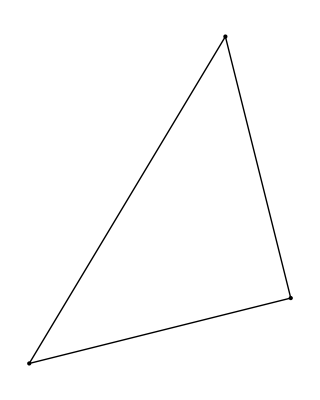

```mathematica
trikotnik1 = Trikotnik[{0,0},{4,1},{3,5}]
Stranice[Trikotnik[AA_, BB_, CC_]] := {Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}
Koti[Trikotnik[AA_, BB_, CC_]] := {Kot[CC, AA, BB],Kot[AA, BB, CC],Kot[BB, CC, AA]}
SlikaOglisc[Trikotnik[AA_, BB_, CC_]]:={Point[AA], Point[BB], Point[CC]}
SlikaStranic[Trikotnik[AA_, BB_, CC_]]:={Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}] }
NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
Stranice[trikotnik1]
Koti[trikotnik1]
SlikaOglisc[trikotnik1]
SlikaStranic[trikotnik1]
NarisiTrikotnik[trikotnik1]
```

Pravoktni trikotnik je trikotnik, z oglišči A, B in C, ki ima en pravi kot in dva topa kota, katerih vsota je 90 °.  Če predpostavimo, da je pravi kot (90 °) kot γ, potem lahko rečemo, da sta kota α in β komplementarna. To pomeni, da je njuna vsota 90 °. Prav tako vemo, da sta stranici a in b kateti, ker ležita ob pravem kotu, stranica c pa je hipotenuza, saj leži nasproti pravega kota. 
      
 1.1 KOTNE FUNKCIJE
V pravokotnem trikotniku lahko za računanje uporabljamo kotne funkcije. Poznamo 4 kotne funkcije.
 - Sinus x

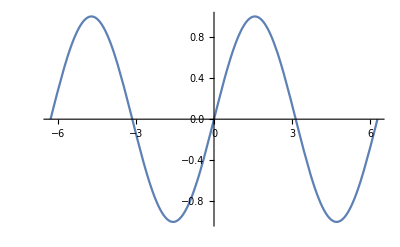

```mathematica
graf1 = Plot[Sin[x], {x, -2Pi,2Pi}]
```

- Kosinus x

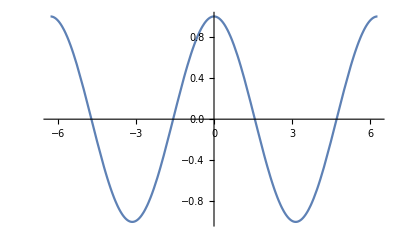

```mathematica
graf2 = Plot[Cos[x],{x, -2Pi,2Pi}]
```

-Tangens x

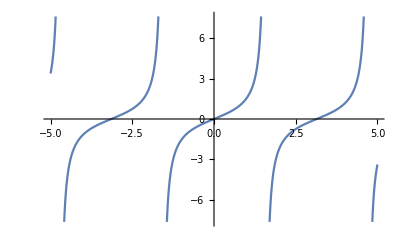

```mathematica
graf3 = Plot[Tan[x],{x,-5,5}]
```

- Kotangens x

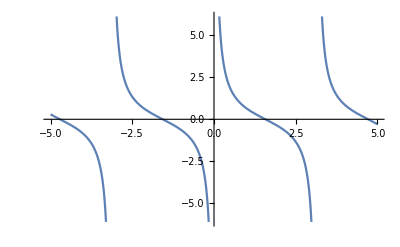

```mathematica
graf4 = Plot[Cot[x],{x,-5,5}]
```

1.2 IZREKI V PRAVOKOTNEM TRIKOTNIKU
 -Evklidov izrek:
 Definicija: Kvadrat katete je enak produktu hipotenuze in pravokotne projekcije te katete na hipotenuzo.

```mathematica
a^2 = Subscript[a, 1] * c
```

-Višinski izrek:
Definicija: Kvadrat višine na hipotenuzo je enak produktu pravokotnih projekcij obeh katet.

```mathematica
v^2 = Subscript[a, 1] * Subscript[b, 1]
```

-Talesov izrek:
Definicija: Središče očrtanega kroga se nahaja točno na sredini hipotenuze, njegov polmer pa je enak polovici hipotenuze.

```mathematica
r = c/2
```

-Pitagorov izrek: 
Definicija: Kvadrat hipotenuze je enak vsoti kvadratov obeh katet.

```mathematica
v^2 = a^2 + b^2
```

1.3 OBSEG IN PLOŠČINA PRAVOKOTNEGA TRIKOTNIKA

```mathematica
o = a + b + c
S = (a * b)/2
```

2. ENAKOSTRANIČNI TRIKOTNIK

```mathematica
trikotnik2 = Manipulate[Graph3D[{A->B, B->C,C->A}, VertexLabels->"Name"], {A}]
```

Enakostranični trikotnik je trikotnik, pri katerem so vse strancie enako dolge. Vsi notranju koti so enaki in imajo 60 °. Višina na katerokoli stranico je enaka. Izračuna se jo po spodaj navedeni formuli.

```mathematica
v = (a * √3)/2
```

2.1 OČRTAN KROG, VČRTAN KROG IN TEŽIŠČE

Enakostraničnemu trikotniku lahko očrtamo ali včrtamo krog. Težišče trikotnika je presečišče vseh treh težiščnic trikotnika. Težiščnica je daljica, ki razpolavlja stranico in ne razpolavlja kota. Središče včrtanega in očrtanega kroga ter težišče se ujemajo v eni točki, ki leži na nosilki višine na stranico. 

Polmer očrtanega kroga:

```mathematica
R = (a * √3)/3
```

Polmer včrtanega kroga:

```mathematica
r = (a * √3)/6
```

Povezava med polmerom očrtanega in včrtanega kroga:

```mathematica
R = 2 * r
```

2.2 OBSEG IN PLOŠČINA ENAKOSTRANIČNEGA TRIKOTNIKA

```mathematica
o = 3 * a
S = (a^2* √3)/4
```

3. ENAKOKRAKI TRIKOTNIK

Trikotnik[{0,0},{1,2},{3,3}]

{Daljica[{0,0},{1,2}],Daljica[{1,2},{3,3}],Daljica[{3,3},{0,0}]}

{Kot[{3,3},{0,0},{1,2}],Kot[{0,0},{1,2},{3,3}],Kot[{1,2},{3,3},{0,0}]}

{Point[{0,0}],Point[{1,2}],Point[{3,3}]}

{Line[{{0,0},{1,2}}],Line[{{1,2},{3,3}}],Line[{{3,3},{0,0}}]}

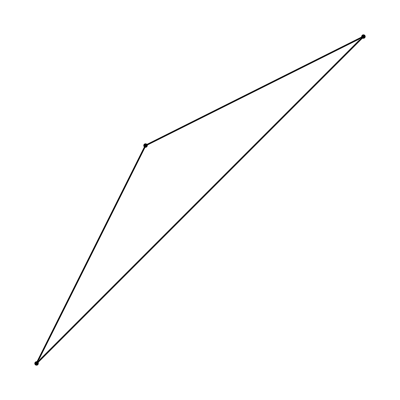

```mathematica
trikotnik3 = Trikotnik[{0,0},{1,2},{3,3}]
Stranice[Trikotnik[AA_, BB_, CC_]] := {Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}
Koti[Trikotnik[AA_, BB_, CC_]] := {Kot[CC, AA, BB],Kot[AA, BB, CC],Kot[BB, CC, AA]}
SlikaOglisc[Trikotnik[AA_, BB_, CC_]]:={Point[AA], Point[BB], Point[CC]}
SlikaStranic[Trikotnik[AA_, BB_, CC_]]:={Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}] }
NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
Stranice[trikotnik3]
Koti[trikotnik3]
SlikaOglisc[trikotnik3]
SlikaStranic[trikotnik3]
NarisiTrikotnik[trikotnik3]
```

Enakokraki trikotnik je trikotnik, ki ima dve stranici skladni. Ti dve stranici se imenujeta kraka, tretja stranica pa je osnovnica. Skupno oglišče krakov se imenuje vrh enakokrakega trikotnika. Višina trikotnika je težišnica na osnovnico in razpolavlja kot pri vrhu.

3.1 OBSEG IN PLOŠČINA

```mathematica
o = a + b + c
S = (a * Subscript[v, a])/2 = (b * Subscript[v, b])/2 = (c * Subscript[v, c])/2
S = (a * b * Sin[γ])/2 = (a * c * Sin[β])/2 = (b * c * Sin[α])/2
```

Ploščino lahko izračunamo tudi s pomočjo Heronovega obrazca:

```mathematica
S = √(s * (s - a) * (s - b) * (s - c))
s = (a + b + c)/2
```

4. POLJUBNI TRIKOTNIK

Trikotnik[{0,0},{3,2},{3,3}]

{Daljica[{0,0},{3,2}],Daljica[{3,2},{3,3}],Daljica[{3,3},{0,0}]}

{Kot[{3,3},{0,0},{3,2}],Kot[{0,0},{3,2},{3,3}],Kot[{3,2},{3,3},{0,0}]}

{Point[{0,0}],Point[{3,2}],Point[{3,3}]}

{Line[{{0,0},{3,2}}],Line[{{3,2},{3,3}}],Line[{{3,3},{0,0}}]}

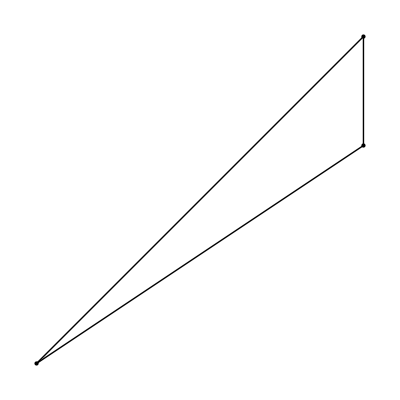

```mathematica
trikotnik4 = Trikotnik[{0,0},{3,2},{3,3}]
Stranice[Trikotnik[AA_, BB_, CC_]] := {Daljica[AA, BB], Daljica[BB, CC], Daljica[CC, AA]}
Koti[Trikotnik[AA_, BB_, CC_]] := {Kot[CC, AA, BB],Kot[AA, BB, CC],Kot[BB, CC, AA]}
SlikaOglisc[Trikotnik[AA_, BB_, CC_]]:={Point[AA], Point[BB], Point[CC]}
SlikaStranic[Trikotnik[AA_, BB_, CC_]]:={Line[{AA, BB}], Line[{BB, CC}], Line[{CC, AA}] }
NarisiTrikotnik[t_Trikotnik]:=Graphics[{SlikaOglisc[t], SlikaStranic[t]}, AspectRatio->Automatic]
Stranice[trikotnik4]
Koti[trikotnik4]
SlikaOglisc[trikotnik4]
SlikaStranic[trikotnik4]
NarisiTrikotnik[trikotnik4]
```

Poljubni trikotnik je trikotnik, ki ima vse tri stranice poljubno dolge. Vsi notranji koti so poljubno veliki, vendar vsota notranjih kotov ne presega 180 °.  

4.1 IZREKI V POLJUBNEM TRIKOTNIKU
- Sinusni izrek:

```mathematica
2 * R = a/Sin[α] = b/Sin[β] = c/Sin[γ]
```

- Kosinusni izrek:

```mathematica
a^2 = b^2 + c^2 - 2 * b * c * Cos[α]
b^2 = a^2 + c^2 - 2 * a * c * Cos[β]
c^2 = a^2 + b^2 - 2 * a * b * Cos[γ]
```

4.2 OČRTAN IN VČRTAN KROG
Polmer očrtanega kroga:

```mathematica
R = (a * b * c)/(4 * S)
```

Polmer včrtanega kroga:

```mathematica
r = S/s
s = (a + b + c)/2 = o/2
```

4.3 OBSEG IN PLOŠČINA

```mathematica
o = a + b + c
S = (a * Subscript[v, a])/2 = (b * Subscript[v, b])/2 = (c * Subscript[v, c])/2
S = (a * b * Sin[γ])/2 = (a * c * Sin[β])/2 = (b * c * Sin[α])/2
```

Tudi pri poljubnem trikotniku lahko ploščino izračunamo tudi s pomočjo Heronovega obrazca:

```mathematica
S = √(s * (s - a) * (s - b) * (s - c))
s = (a + b + c)/2
```

5. NALOGA NA TEMO TRIKOTNIKOV
Kot α v pravokotnem trikotniku meri 37 °, dolžina hipotenuze c pa je 4.98 cm. Izračunaj obseg in ploščino trikotnika.
Formula za izračun obsega:

```mathematica
α = 37 °
c = 4.98
o = a + b + c
```

Da lahko izračuna obseg trikotnika, moramo prvo izračunati še stranici a in b.

```mathematica
Sin[α] = a/c
a = c * Sin[α]
```

0.6

```mathematica
a = 4.98 * 0.60
```

2.988

Stranico b bomo izračunali s pomočjo pitagorovega izreka.

```mathematica
b^2 = c^2 - a^2
```

```mathematica
b = √(4.98^2 - 2.988^2)
```

3.984

Sedaj lahko izračunamo obseg trikotnika.

```mathematica
o = a + b + c
o = (2.988 + 3.984 + 4.98) cm
```

11.952 cm

Ploščino izračunamo po naslednji enačbi.

```mathematica
S = (a * b)/2
S = ((2.988 * 3.984)/2)cm^2
```

5.9521 cm^2